## Introduction

Chaos 2

## Main

### Method

```mathematica
run[k_]:=Block[{dt,n,T,J,e,b,b1,b2,Ex,Eθ,Wp,Wm,t,NT},
(*Preamble*)
{dt,n,T}={0.1,100,1000}; 
{J}={1};
{e,b}={1.9,2};

{Ex,Eθ} = {e,e};
{b1,b2} = {b,b};

{z0,pin,znew}={Table[RandomReal[{0,2π}],{i,1,2},{j,1,n}],Table[RandomReal[{0,2π}],{i,1,2},{j,1,n}],ConstantArray[0,{2,n}]}; (*z = [x,θ]*)
pin=Table[Table[2 Pi i / (n-1),{i,0,n-1}]//N,{j,1,2}];
z00 = z0;

(*{z0,znew}={Table[RandomReal[{0,π}],{i,1,2},{j,1,n}],ConstantArray[0,{2,n}]};*) (*Use these to see the static sync states*)

{t,NT}={0,Floor[T/dt]} ; (*T = number of timesteps*)

(*Main sim*)
{Wp,Wm}={{},{}};
While[t<NT,
znew=rk4[z0,rhs,dt,J,k,Ex,Eθ,pin,b1,b2];
z0=znew;t++;
{Wp1,Wm1}=findWs[znew];
AppendTo[Wp,Wp1];AppendTo[Wm,Wm1];
];

p0=plotResults[znew,pin];
Print[p0];

cutoff=Round[0.5 Length[Wp]];
p1=ListPlot[{Abs[Wp],Abs[Wm]},AxesLabel->{"t"},PlotLegends->{"S+","S-"},LabelStyle->15,Joined->True,ImageSize->Medium,PlotLabel->"{J,K,E} = "<>ToString[{J,k,e}]];
p2=ListPlot[{Wp[[cutoff;;-1]]//Re,Wp[[cutoff;;-1]]//Im}ᵀ,AxesLabel->{"t"},LabelStyle->15,Joined->True,ImageSize->Medium,PlotRange->{{-1.1,1.1},{-1.1,1.1}},AxesLabel->{"Re(W+)","Im(W+)"}];
p3=ListPlot[{Wm[[cutoff;;-1]]//Re,Wm[[cutoff;;-1]]//Im}ᵀ,AxesLabel->{"t"},LabelStyle->15,Joined->True,ImageSize->Medium,PlotRange->{{-1.1,1.1},{-1.1,1.1}},AxesLabel->{"Re(W-)","Im(W-)"}];
Return[Grid[{{p1,p2,p3}}]]
]
```

### Explore

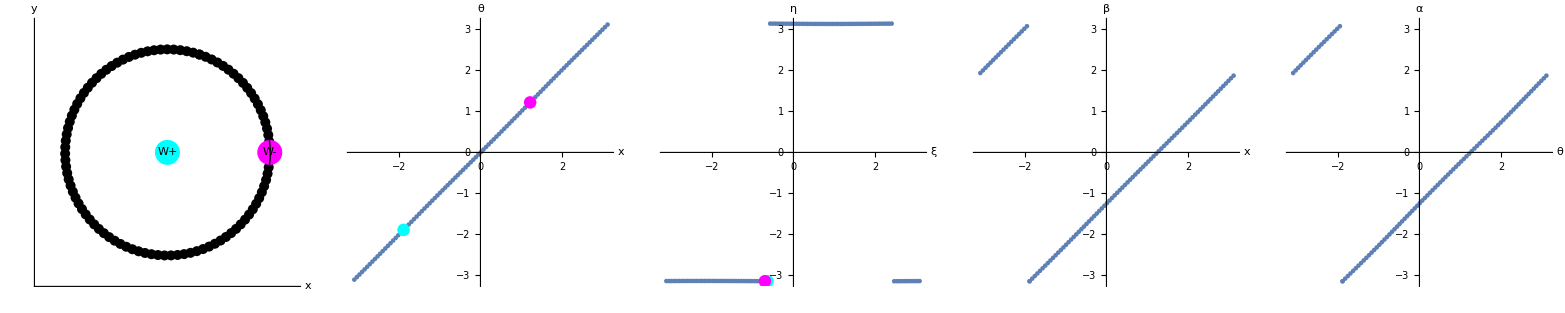

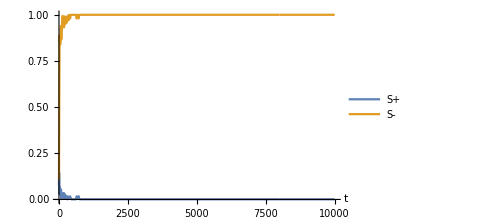
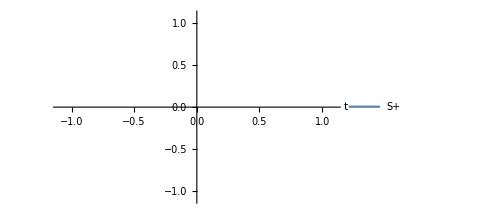
-Graphics- | -Graphics- | -Graphics-

```mathematica
run[-2.0]
```

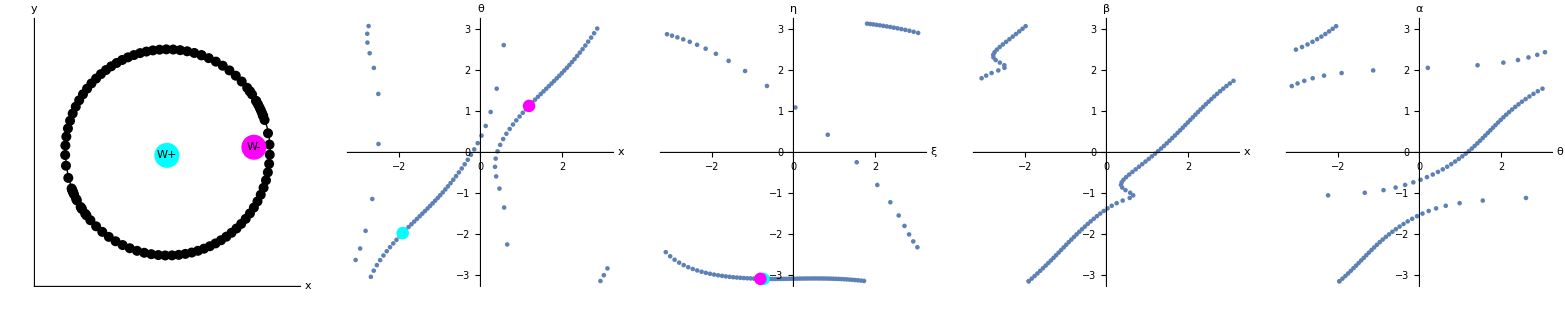

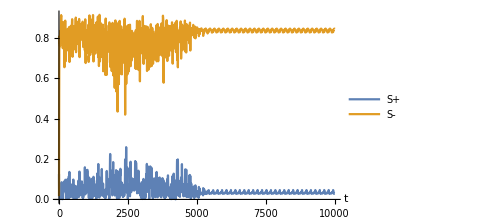
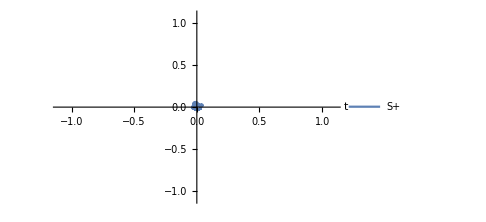
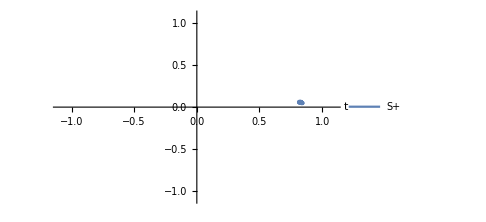
-Graphics- | -Graphics- | -Graphics-

```mathematica
run[-2.5]
```

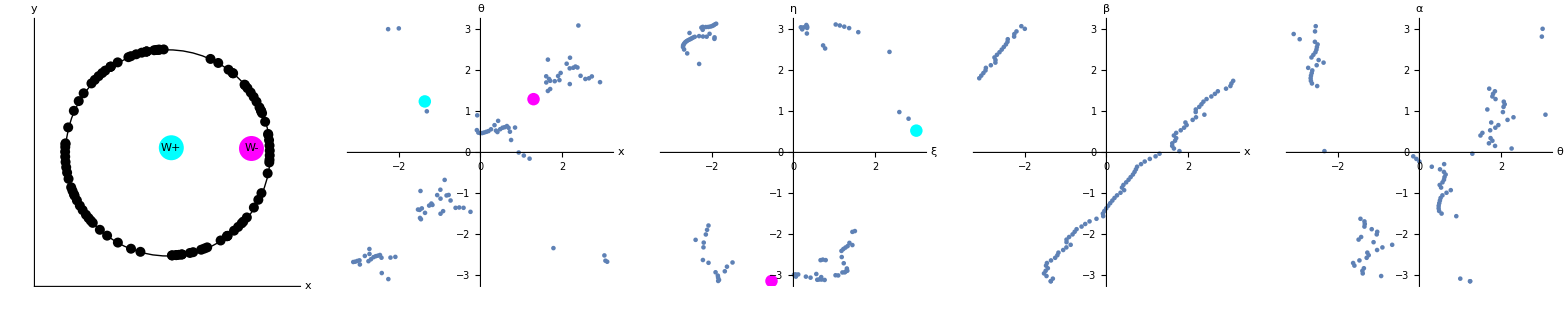

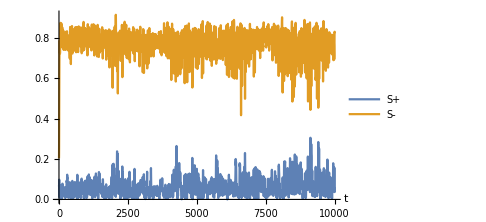
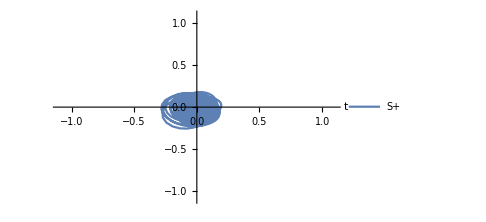
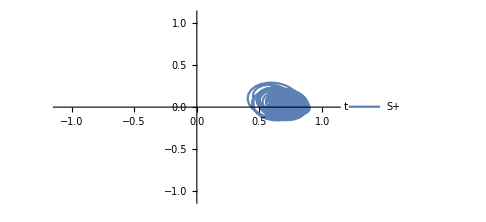
-Graphics- | -Graphics- | -Graphics-

```mathematica
run[-2.65]
```

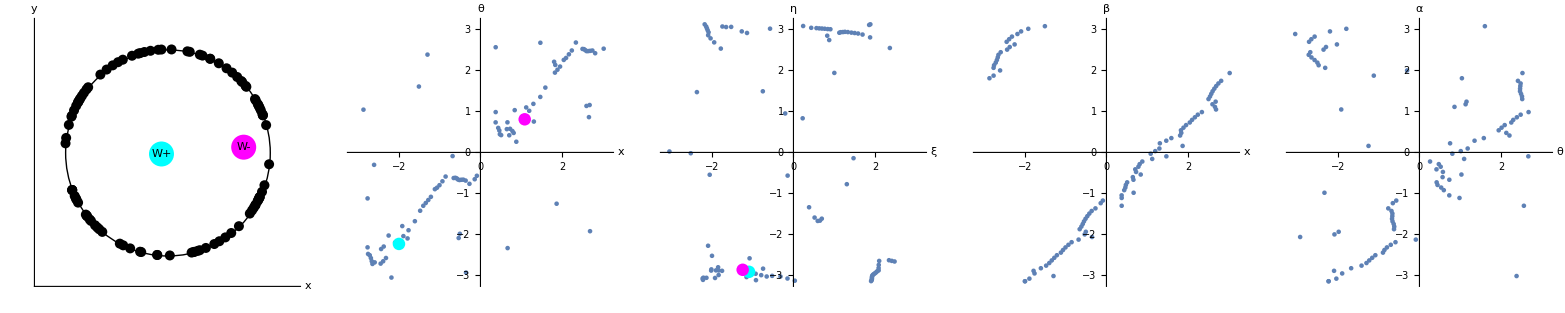

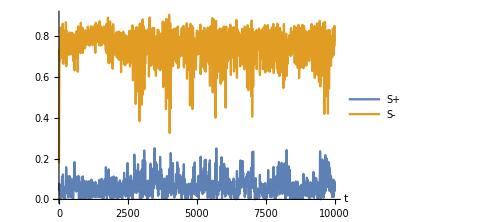
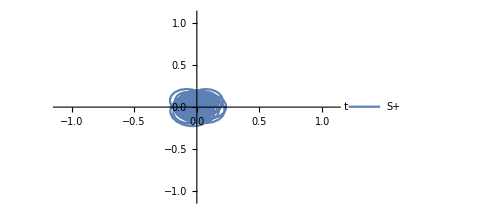
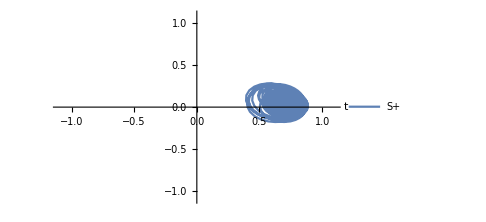
-Graphics- | -Graphics- | -Graphics-

```mathematica
run[-2.7]
```

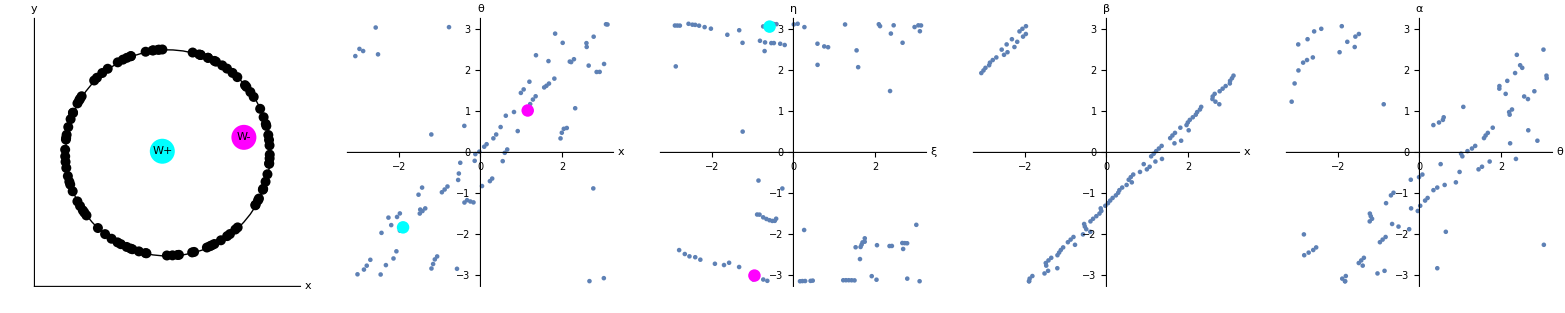

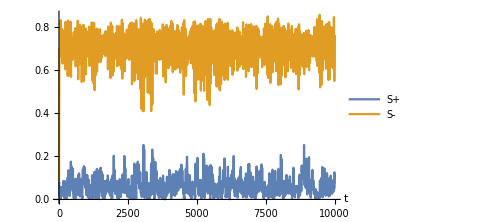
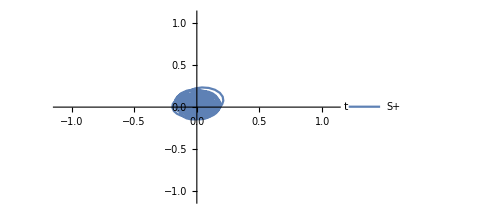
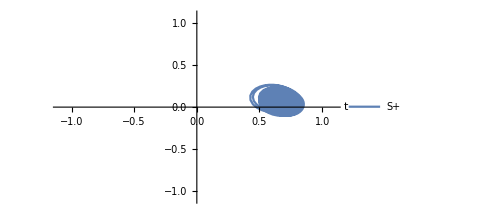
-Graphics- | -Graphics- | -Graphics-

```mathematica
run[-3.0]
```

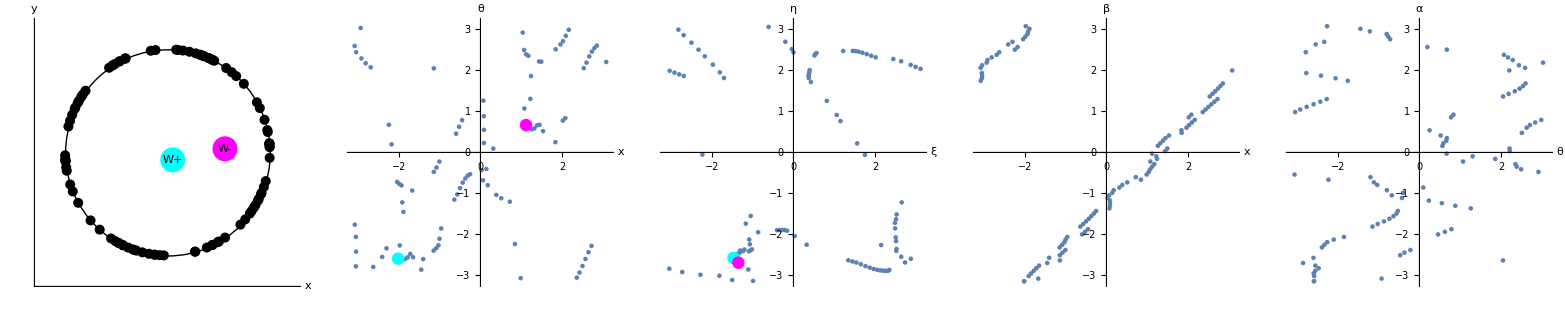

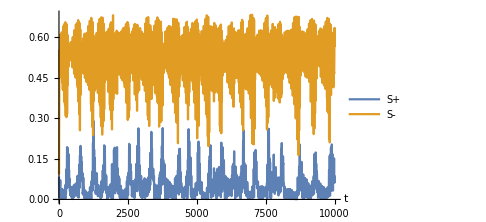
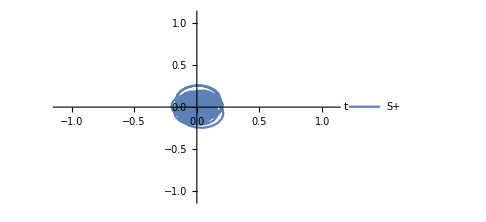
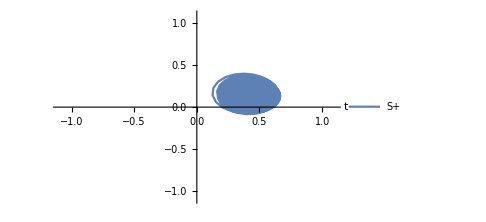
-Graphics- | -Graphics- | -Graphics-

```mathematica
run[-5.0]
```

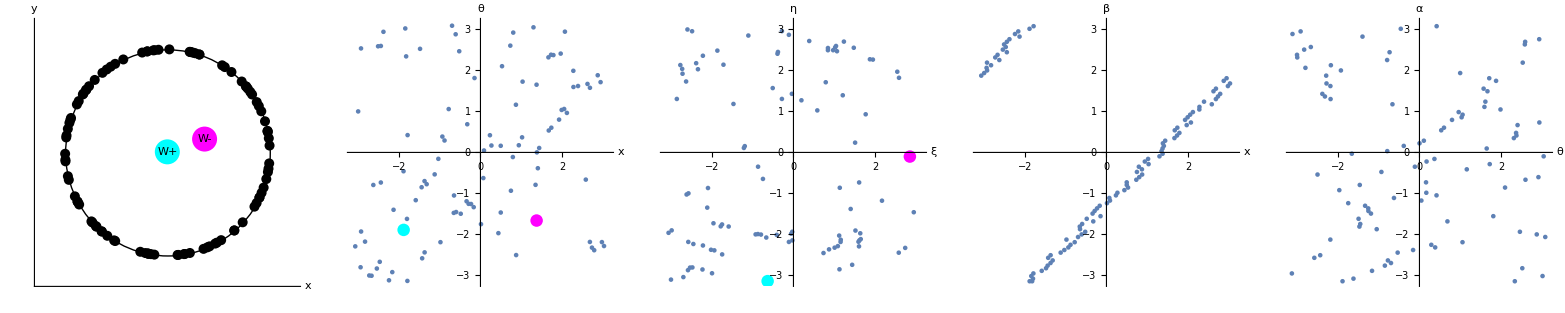

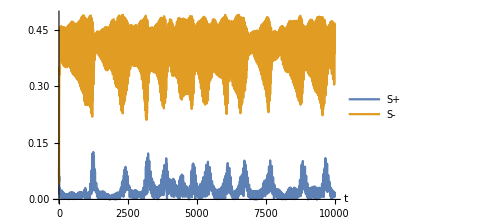
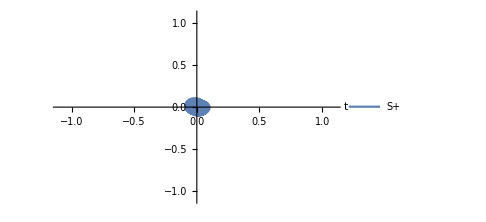
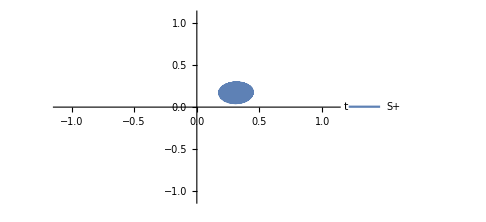
-Graphics- | -Graphics- | -Graphics-

```mathematica
run[-8.0]
```

## Period doubling

### Method

```mathematica
run[k_]:=Block[{dt,n,T,J,e,b,b1,b2,Ex,Eθ,Wp,Wm,t,NT},
(*Preamble*)
{dt,n,T}={0.1,200,500}; 
{J}={1};
{e,b}={1.9,2};

{Ex,Eθ} = {e,e};
{b1,b2} = {b,b};

{z0,pin,znew}={Table[RandomReal[{0,2π}],{i,1,2},{j,1,n}],Table[RandomReal[{0,2π}],{i,1,2},{j,1,n}],ConstantArray[0,{2,n}]}; (*z = [x,θ]*)
pin=Table[Table[2 Pi i / (n-1),{i,0,n-1}]//N,{j,1,2}];
z00 = z0;

(*{z0,znew}={Table[RandomReal[{0,π}],{i,1,2},{j,1,n}],ConstantArray[0,{2,n}]};*) (*Use these to see the static sync states*)

{t,NT}={0,Floor[T/dt]} ; (*T = number of timesteps*)

(*Main sim*)
{Wp,Wm}={{},{}};
While[t<NT,
znew=rk4[z0,rhs,dt,J,k,Ex,Eθ,pin,b1,b2];
z0=znew;t++;
{Wp1,Wm1}=findWs[znew];
AppendTo[Wp,Wp1];AppendTo[Wm,Wm1];
];

p0=plotResults[znew,pin];
(*Print[p0];*)

cutoff=Round[0.5 Length[Wp]];
p1=ListPlot[{Abs[Wp],Abs[Wm]},AxesLabel->{"t"},PlotLegends->{"S+","S-"},LabelStyle->15,Joined->True,ImageSize->Medium,PlotLabel->"{J,K,E} = "<>ToString[{J,k,e}]];
p2=ListPlot[{{Wp[[cutoff;;-1]]//Re,Wp[[cutoff;;-1]]//Im}ᵀ,{Wm[[cutoff;;-1]]//Re,Wm[[cutoff;;-1]]//Im}ᵀ},LabelStyle->15,Joined->True,ImageSize->Medium,PlotRange->{{-1.1,1.1},{-1.1,1.1}},AxesLabel->{"Re","Im"},PlotLabel->"{J,K,E} = "<>ToString[{J,k,e}],PlotLegends->{"W+","W0"}];
Return[p2]
]
```

### Plots

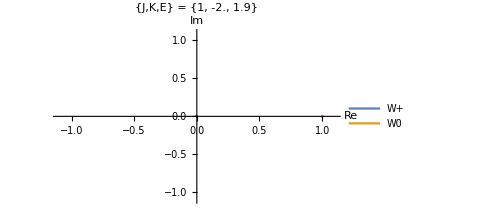
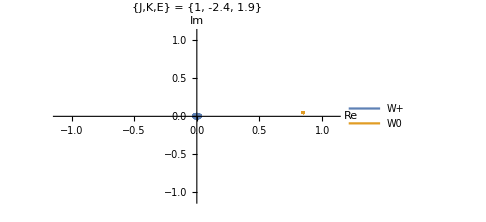
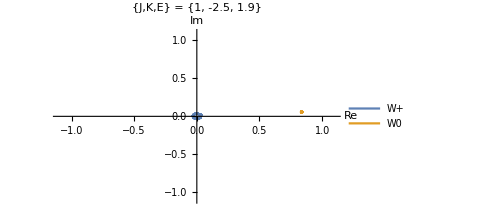
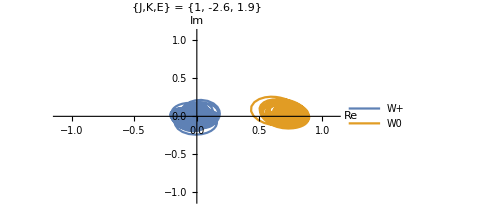
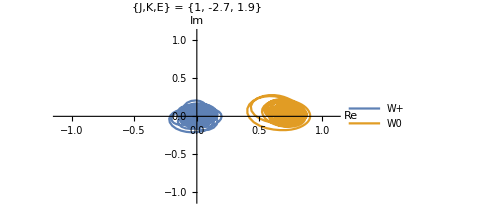
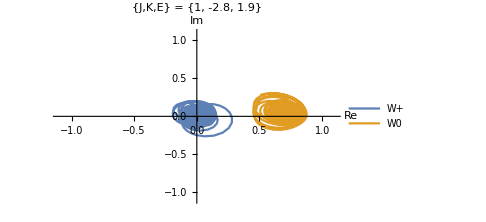
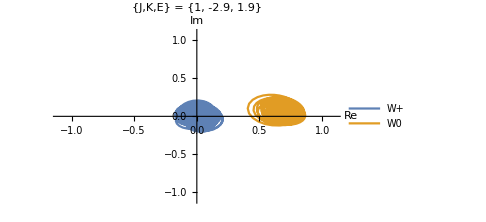
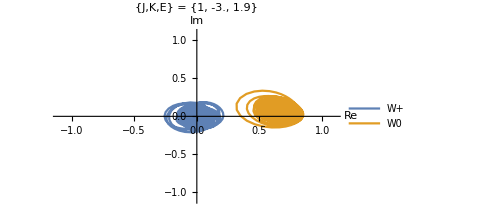
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-

```mathematica
ks={-2.0,-2.4,-2.5,-2.6,-2.7,-2.8,-2.9,-3.0,-5.0};
figs=Table[run[k],{k,ks}];
Grid[Partition[figs,4]]
```

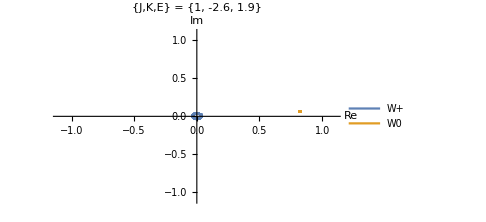
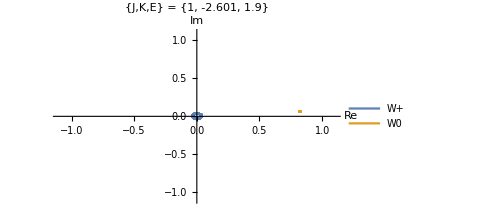
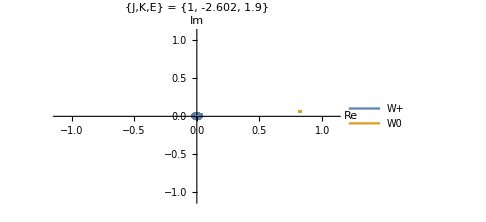
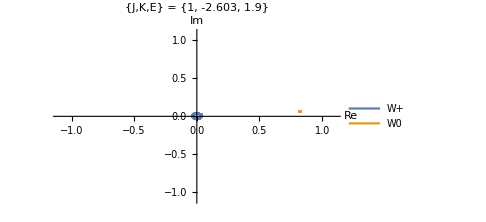
-Graphics- | -Graphics- | -Graphics- | -Graphics-

```mathematica
ks=Table[k,{k,-2.6,-2.605,-0.001}];
figs=Table[run[k],{k,ks}];
Grid[Partition[figs,4]]
```

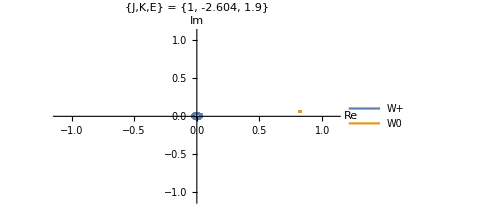
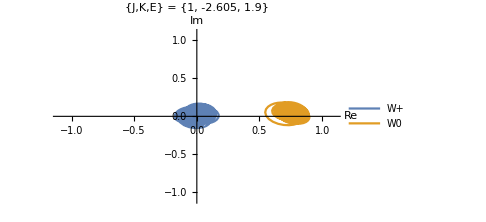
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
figs
```

## Functions

```mathematica
rhs=Compile[{{z,_Real,2},{n,_Integer},{J,_Real},{k,_Real}, {Ex,_Real}, {Eθ, _Real}, {pin, _Real, 2}, {b1,_Real},{b2,_Real}},
Module[{i,j,xji,yji,thetaji,inverseDistSq,inverseDist,xtemp,ytemp,thetatemp,rep,A,B,C,n1,vel=ConstantArray[0.0,{2,n}]},
{A,B,C,n1}={1,1,10,1};
For[i=1,i≤n,i++,
vel[[1,i]] = Ex + b1*Sin[pin[[1,i]] - z[[1,i]]];
vel[[2,i]] = Eθ + b2*Sin[pin[[2,i]] - z[[2,i]]];
];
For[i=1,i≤n,i++,
For[j=i+1,j≤n,j++,
xji=z[[1,j]]-z[[1,i]];
thetaji=z[[2,j]]-z[[2,i]];
xtemp=J*Sin[xji]*Cos[thetaji]/N[n];
thetatemp=k*Sin[thetaji]*Cos[xji]/N[n];
vel[[1,i]]+=xtemp;vel[[1,j]]+=-xtemp;
vel[[2,i]]+=thetatemp;vel[[2,j]]+=-thetatemp;
];
];
vel
(*vel/N[n]*)
],
RuntimeAttributes->Listable,
Parallelization->True,
CompilationTarget->"C"
];

findWs[z_]:=Block[{Wp,Wm,i,numOsc},
{Wp,Wm}={0,0};
numOsc=Length[z[[1]]];
For[i=1,i≤numOsc,i++,
Wp+=Exp[ⅈ (z[[1,i]]+z[[2,i]])];
Wm+=Exp[ⅈ (z[[1,i]]-z[[2,i]])];
];
Return[{Wp/numOsc,Wm/numOsc}]
]

plotResults[z_,pin_]:=Block[{colors,Wp,Wm,p1,p2,p3,p4,p5,x,θ,xin,θin},
{x,θ}={z[[1,All]],z[[2,All]]};
{xin,θin}={pin[[1,All]],pin[[2,All]]};
colors=ColorData["VisibleSpectrum"]/@((750-380)(Mod[θ,2π]-1)/(2π)+380);
{Wp,Wm}=findWs[z];

p1=Graphics[{
(*Swarmalators*)
PointSize[0.02],Point[{Cos[z[[1,All]]],Sin[z[[1,All]]]}ᵀ,VertexColors->colors],

(*Order parameters*)
PointSize[0.05],

Cyan,Point[{Wp//Re,Wp//Im}],Black,Text["W+",{Wp//Re,Wp//Im}],
Magenta,Point[{Wm//Re,Wm//Im}],Black,Text["W-",{Wm//Re,Wm//Im}],

Black,Circle[{0,0},1]
},
PlotRange->{{-1.25,1.25},{-1.25,1.25}},Axes->True,Ticks->None,AspectRatio->1,AxesLabel->{"x","y"},LabelStyle->20,ImageSize->Medium];


(*Scatter plot in (x,theta) space*)
p2=ListPlot[{x//mod,θ//mod}ᵀ,PlotRange->{{-π,π},{-π,π}},ImageSize->Medium,AxesLabel->{Style["x",15],Style["θ",15]}];

(*Scatter plot in (ξ,θ) space*)
p3=ListPlot[{x+θ,x-θ}ᵀ//mod,PlotRange->{{-π,π},{-π,π}},ImageSize->Medium,AxesLabel->{Style["ξ",15],Style["η",15]}];

p4=ListPlot[{x,xin}ᵀ//mod,PlotRange->{{-π,π},{-π,π}},ImageSize->Medium,AxesLabel->{Style["x",15],Style["β",15]}];

p5=ListPlot[{θ,θin}ᵀ//mod,PlotRange->{{-π,π},{-π,π}},ImageSize->Medium,AxesLabel->{Style["θ",15],Style["α",15]}];

Return[Grid[{{p1,p2,p3,p4,p5}}]
]
];


eulerStep[z_,F_,dt_,J_,k_,Ex_,Eθ_,pin_,b1_,b2_]:=Block[{znew,n,i,j,vel},
znew=ConstantArray[0,Dimensions[z]];
n=Dimensions[z][[2]];
vel=F[z,n,J,k,Ex,Eθ,pin,b1,b2];
znew=z+dt*vel;
Return[znew]
];

rk4[z_,F_,dt_,J_,k_,Ex_,Eθ_,pin_,b1_,b2_]:=Block[{znew,n,i,j,k1,k2,k3,k4},
znew=ConstantArray[0,Dimensions[z]];
n=Dimensions[z][[2]];
k1=F[z,n,J,k,Ex,Eθ,pin,b1,b2];
k2=F[z+dt/2 k1,n,J,k,Ex,Eθ,pin,b1,b2];
k3=F[z+dt/2 k2,n,J,k,Ex,Eθ,pin,b1,b2];
k4=F[z+dt k3,n,J,k,Ex,Eθ,pin,b1,b2];
Return[z+dt/6(k1+2k2+2k3+k4)]
];

mod[θ_]:=Return[Mod[θ,2π]-π];

findMeanV[znew_,z_,dt_]:=Block[{v},
v=(znew-z)/dt;
v=(v[[1,All]]^2+v[[2,All]]^2)^(1/2);
Return[Mean[v]]
];

findGamma[xs_,θs_,cutoff_]:=Block[{gammas,i,n,x,θ,xSteady,rangeSteadyX,gammaX,θSteady,rangeSteadyθ,gammaθ,index},
(*Find fraction of swarmalators that have completed at least 
 one full oscillation (0,2π) mod 2π, after transients have been discarded *)

n= Dimensions[xs][[2]];
gammas={};
For[i=1,i≤n,i++,
{x,θ}={xs[[All,i]],θs[[All,i]]};

(*Check for one loop when x has approximately achieved its steady state*)
xSteady=x[[cutoff;;-1]];
rangeSteadyX=Max[xSteady]-Min[xSteady];
gammaX=If[rangeSteadyX>=2π,1,0];

(*Check for one loop when θ has approximately achieved its steady state*)
θSteady=θ[[cutoff;;-1]];
rangeSteadyθ=Max[θSteady]-Min[θSteady];
gammaθ=If[rangeSteadyθ>=2π,1,0];

(*Require both to be true*)
AppendTo[gammas,gammaX*gammaθ]
];

(*Return fraction of swarmalators with gamma = 1*)
Return[Mean[gammas]]
];

plotResults[z_,pin_]:=Block[{colors,Wp,Wm,p1,p2,p3,p4,p5,x,θ,xin,θin,x1,θ1,x2,θ2,ξ1,ξ2,η1,η2,index,n},
{x,θ}={z[[1,All]],z[[2,All]]};
{xin,θin}={pin[[1,All]],pin[[2,All]]};
colors=ColorData["VisibleSpectrum"]/@((750-380)(Mod[θ,2π]-1)/(2π)+380);
{Wp,Wm}=findWs[z];

p1=Graphics[{
(*Swarmalators*)
PointSize[0.02],Point[{Cos[z[[1,All]]],Sin[z[[1,All]]]}ᵀ,VertexColors->colors],

(*Order parameters*)
PointSize[0.05],

Cyan,Point[{Wp//Re,Wp//Im}],Black,Text["W+",{Wp//Re,Wp//Im}],
Magenta,Point[{Wm//Re,Wm//Im}],Black,Text["W-",{Wm//Re,Wm//Im}],

Black,Circle[{0,0},1]
},
PlotRange->{{-1.25,1.25},{-1.25,1.25}},Axes->True,Ticks->None,AspectRatio->1,AxesLabel->{"x","y"},LabelStyle->20,ImageSize->Medium];


(*Scatter plot in (x,theta) space*)
n=Length[x];
index=Round[n/2];
{x1,θ1}={x[[1]],θ[[1]]};
{x2,θ2}={x[[index]],θ[[index]]};
p2=ListPlot[{x//mod,θ//mod}ᵀ,PlotRange->{{-π,π},{-π,π}},ImageSize->Medium,AxesLabel->{Style["x",15],Style["θ",15]},Epilog->{Cyan,PointSize[0.025],Point[{x1,θ1}//mod],Magenta,Point[{x2,θ2}//mod]}];

(*Scatter plot in (ξ,θ) space*)
{ξ1,η1}={x[[1]]+θ[[1]],x[[1]]-θ[[1]]};
{ξ2,η2}={x[[index]]+θ[[index]],x[[index]]-θ[[index]]};
p3=ListPlot[{x+θ,x-θ}ᵀ//mod,PlotRange->{{-π,π},{-π,π}},ImageSize->Medium,AxesLabel->{Style["ξ",15],Style["η",15]},Epilog->{Cyan,PointSize[0.025],Point[{ξ1,η1}//mod],Magenta,Point[{ξ2,η2}//mod]}];

p4=ListPlot[{x,xin}ᵀ//mod,PlotRange->{{-π,π},{-π,π}},ImageSize->Medium,AxesLabel->{Style["x",15],Style["β",15]}];

p5=ListPlot[{θ,θin}ᵀ//mod,PlotRange->{{-π,π},{-π,π}},ImageSize->Medium,AxesLabel->{Style["θ",15],Style["α",15]}];

Return[Grid[{{p1,p2,p3,p4,p5}}]
]
];
```